```mathematica
a={{.9925,.0125},{.0075,.9875}}
```

{{0.9925,0.0125},{0.0075,0.9875}}

```mathematica
Eigensystem[a]
```

{{1.,0.98},{{0.857493,0.514496},{-0.707107,0.707107}}}

```mathematica
eigenvalues=Eigensystem[a][[1]]
eigenvectors=Eigensystem[a][[2]]
MatrixForm[eigenvectors]
```

{1.,0.98}

{{0.857493,0.514496},{-0.707107,0.707107}}

(0.857493 | 0.514496
-0.707107 | 0.707107)

```mathematica
initial={10,990}
```

{10,990}

```mathematica
coeff=LinearSolve[Transpose[eigenvectors],initial]
```

{728.869,869.741}

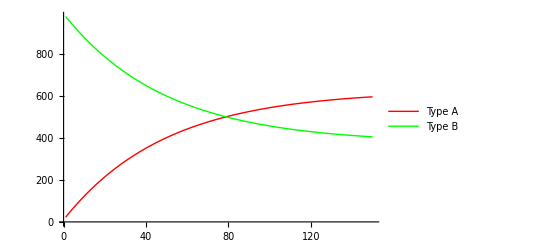

```mathematica
t[n_]:=coeff[[1]](eigenvalues[[1]]^n)eigenvectors[[1]]+coeff[[2]](eigenvalues[[2]]^n)eigenvectors[[2]];
Plot[{t[n][[1]],t[n][[2]]},{n,1,150},PlotStyle->{Red,Green},PlotLegends->{"Type A", "Type B"}]
```